```mathematica
v={{1,1},{5,4/5},{25,18/25},{125,92/125},{625,446/625},{3125,2199/3125},{15625,11071/15625},{78125,11051/15625},{390625,55283/78125},{1953125,1381869/1953125},{9765625,6908443/9765625},{48828125,34539344/48828125}}
```

{{1,1},{5,4/5},{25,18/25},{125,92/125},{625,446/625},{3125,2199/3125},{15625,11071/15625},{78125,11051/15625},{390625,55283/78125},{1953125,1381869/1953125},{9765625,6908443/9765625},{48828125,34539344/48828125}}

```mathematica
Solve[a Log[3,48828125] + b Log[5,48828125] == 34539344/48828125,{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a→(34539344 Log[3])/(48828125 Log[48828125])-(11 b Log[3])/Log[48828125]}}

```mathematica
N[34539344/48828125]/EulerGamma
```

1.22548

```mathematica
N[1/Log[5]]
```

0.621335

```mathematica
N[Log[3]/Log[5]]
```

0.682606

```mathematica
Pi-3.121960844898424
```

0.0196318

```mathematica
Exp[3.121960844898424]
```

22.6908

```mathematica
N[Log[2]/Zeta[15]]
```

0.693126

```mathematica
Solve[N[1/Log[15,a]]==N[34539344/48828125],{a}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→45.987}}

```mathematica
N[(Zeta^(-1))[0.7771207221439518]]
```

Zeta^(-1)[0.777121]

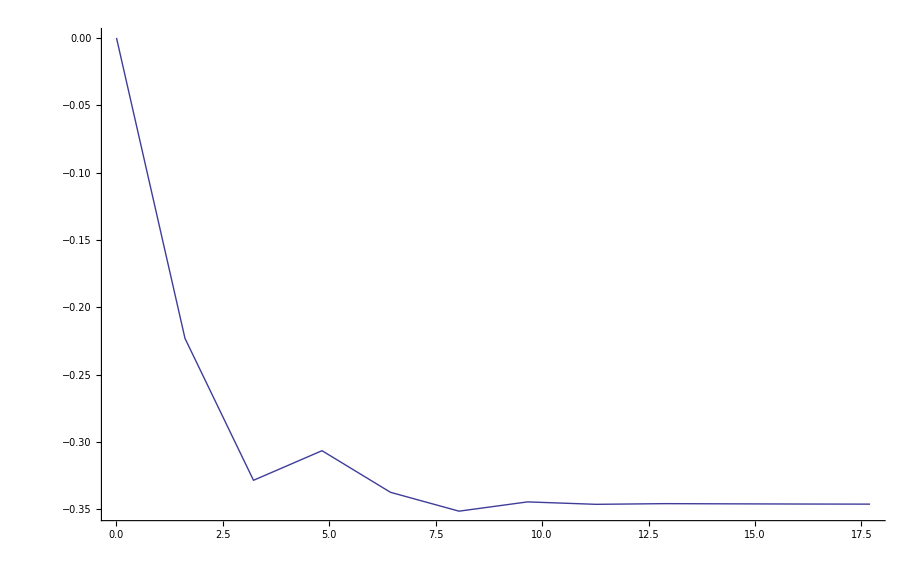

```mathematica
ListPlot[Log[v], Joined->True]
```

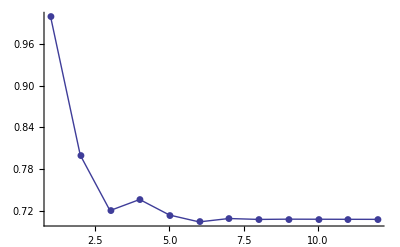

```mathematica
ListPlot[Map[#[[2]]&,v], Joined->True,PlotMarkers->Automatic, PlotRange->All]
```

```mathematica
w=Map[#[[1]]*#[[2]]&,v]
```

{1,4,18,92,446,2199,11071,55255,276415,1381869,6908443,34539344}

```mathematica
Table[ IntegerPart[(Pi-3)5 ^x], {x,1,12}]
```

{0,3,17,88,442,2212,11061,55309,276548,1382740,6913703,34568518}

```mathematica
FindFit[w,(Pi-3)  5^(x+c),{a,b,c},x]
```

{a→1.,b→1.,c→-0.000522411}

```mathematica
FullSimplify[InterpolatingPolynomial[v,x]]
```

1+(-1+x) (-1/20+(-5+x) (23/12000+(-25+x) (-941/62000000+(-125+x) (585937/24180000000000+((-625+x) (-189154154111159463250815542018146101715773693285882472991943359375+x (12605332500242763723142305632783326476747499406337738037109375+x (-162386959564498541976099852989936734229152854919433593750+x (413044667482165682067904908862740524231496386718750+x (-203084590393440729971144705461607443357096875+16637752632122502968464970163802762291 x))))))/19524636490071681411526447657272219657897949218750000000000000000000000000000))))

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
N[Log[3,5^10]]
```

14.6497

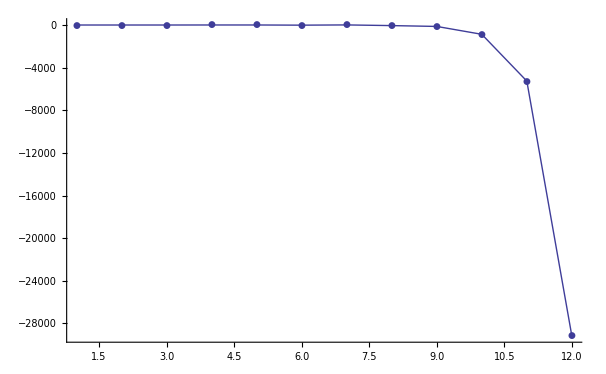

```mathematica
ListPlot[Table[w[[x]]- (Pi-3)5 ^x, {x,1,12}], Joined->True, PlotMarkers->Automatic, Axes->True, PlotRange->All]
```

```mathematica
Golomb
```